```mathematica
SetDirectory[NotebookDirectory[]];
```

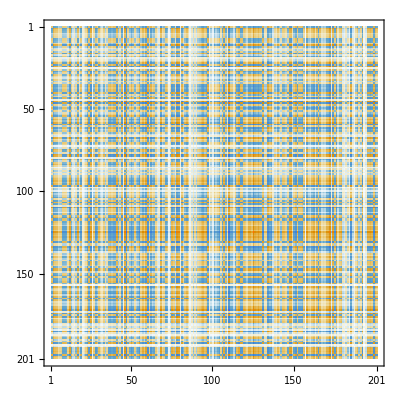

```mathematica
CovMat = (Import["boot_covar.csv"]//Chop[#,10^-12]&)//MatrixPlot
```

```mathematica
ConstantFit=Function[{Y,CovInv},Block[{length,H, ,Δ,δm,m,χsq,dof,χsqpd,CL,LowerLine,MidLine,UpperLine,Plateau,PlateauGraphics,CInv1},length=Length[Y];
CInv1=CovInv.ConstantArray[1,length];
H=2 ConstantArray[1,length].CInv1;
Δ=2/H;
δm=Sqrt[Δ];
m=Δ Y.CInv1;
χsq=(Y-m).CovInv.(Y-m);
dof=length-1;
χsqpd=χsq/dof;
{m,δm,χsqpd}]];
```

```mathematica
?Import
```